### Oriented areas of different shapes

```mathematica
<<peeters` ;
peeters`setGitDir[ "../project/figures/GAelectrodynamics" ]
```

/Users/pjoot/project/figures/GAelectrodynamics

```mathematica
ClearAll[o, e1, e2, unitParallelogram]
o = {0,0};
e1 = {1,0};
e2 = {0,1};
unitParallelogram[or_, v1_,v2_] := Module[{a},a = Abs[Det[{v1,v2}]];
(*{a,v1,v2, {v1/a,v2}}*)
Parallelogram[or, {v1/a,v2}]
 ];
orientedArc[or_,s_, f_, r_,c_] := Module[{data,p},
data=Table[or+r{Cos[x],Sin[x]},{x,s,f, (f-s)/100}];p=ListPlot[data,Frame->True,Axes->False,Joined->True,PlotStyle->{c(*,Thin(*Thick*)*)}, AspectRatio->1];
p/.Line[x_]:>{Arrowheads[{0,.03(*,.05*),0}],Arrow[x]}
];
```

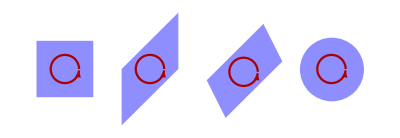

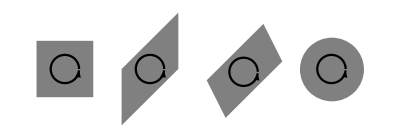

```mathematica
ClearAll[orientedAreasVarietyFig1, bworientedAreasVarietyFig1, f]

f[c1_, c2_] := Show[
{Graphics[
{c1,
unitParallelogram[o, e1,e2] ,
unitParallelogram[1.5 e1-0.5e2, e1 + e2,e2] ,
unitParallelogram[3 e1+0.3e2, e1 - 2e2,e2+e1],
Disk[5.2e1+e2/2,1/Sqrt[Pi]]
}
],
orientedArc[(e1+e2)/2,0,2 Pi-0.1,0.25, c2]
,
orientedArc[1.5 e1+(e1+e2)/2,0,2 Pi-0.1,0.25, c2]
,
orientedArc[3 e1+0.65(e1+e2)-0.2e2,0,2 Pi-0.1,0.25, c2]
,
orientedArc[5.2e1+e2/2,0,2 Pi-0.1,0.25, c2]
}]

orientedAreasVarietyFig1 = f[Blue // Lighter // Lighter, Red //Darker]
bworientedAreasVarietyFig1 = f[Gray, Black]
```

```mathematica
peeters`exportForLatex["orientedAreasVarietyFig1", bworientedAreasVarietyFig1]
```

{orientedAreasVarietyFig1.eps,orientedAreasVarietyFig1pn.png}